```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

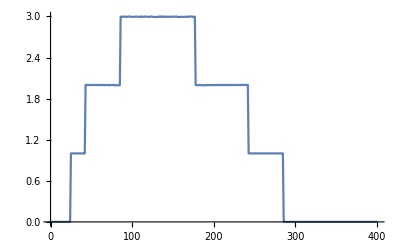

```mathematica
ListLinePlot[Table[tr[ω,0.0001,1,0],{ω,0,4,0.01}]]
```

```mathematica
imp1[ω_,ϵ1_]:=Inverse[Module[{κ=β[ω,0.0001,1,0],μ1=RandomInteger[{1,14}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2[ω_,ϵ2_]:=Inverse[Module[{κ=β[ω,0.0001,1,0],μ2=RandomInteger[{1,14}]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ2]]];imp[ω_,ϵ2_]:=Inverse[Module[{κ=β[ω,0.0001,1,0],μ2=RandomInteger[{1,14}]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-0]]]
```

```mathematica
RandomSample[Join[Table[imp1[ω,ϵ1],14*1],Table[imp2[ω,ϵ2],14*2.5],Table[imp[ω,ϵ2],100-14*3.5]]]
```

{imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2]}

```mathematica
m1025[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1]},
tra1:=Module[{},
b=Module[{},
lista={RandomSample[{imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2]}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>3,3,tra1]]
```

```mathematica
Table[{ω,Mean[Table[m1025[ω,0.3,0.9],2000]]},{ω,Range[0,1.5,0.01]}]
Table[{ω,Mean[Table[m1025[ω,0.9,0.3],2000]]},{ω,Range[0,1.5,0.01]}]
```

{{0.,0.0000419659},{0.01,0.0000335643},{0.02,0.0000344924},{0.03,0.0000424472},{0.04,0.0000708599},{0.05,0.000100722},{0.06,0.000143147},{0.07,0.00019994},{0.08,0.000274764},{0.09,0.000359631},{0.1,0.000475241},{0.11,0.000599334},{0.12,0.000736279},{0.13,0.000878038},{0.14,0.00117233},{0.15,0.00152265},{0.16,0.00186259},{0.17,0.00239966},{0.18,0.00321155},{0.19,0.00412491},{0.2,0.00613427},{0.21,0.00840458},{0.22,0.0133615},{0.23,0.0271527},{0.24,0.0804546},{0.25,0.118445},{0.26,0.144635},{0.27,0.170459},{0.28,0.209896},{0.29,0.24752},{0.3,0.289821},{0.31,0.313563},{0.32,0.337342},{0.33,0.359398},{0.34,0.372845},{0.35,0.371801},{0.36,0.390889},{0.37,0.403216},{0.38,0.415865},{0.39,0.409621},{0.4,0.41271},{0.41,0.44546},{0.42,0.846561},{0.43,1.30987},{0.44,1.11236},{0.45,0.914089},{0.46,0.676292},{0.47,0.566586},{0.48,0.555736},{0.49,0.53029},{0.5,0.510727},{0.51,0.508713},{0.52,0.499194},{0.53,0.511862},{0.54,0.521841},{0.55,0.5468},{0.56,0.55663},{0.57,0.567978},{0.58,0.594691},{0.59,0.580918},{0.6,0.620732},{0.61,0.643479},{0.62,0.653723},{0.63,0.653105},{0.64,0.683905},{0.65,0.686472},{0.66,0.710003},{0.67,0.724921},{0.68,0.730686},{0.69,0.762693},{0.7,0.756844},{0.71,0.768808},{0.72,0.782769},{0.73,0.786366},{0.74,0.848257},{0.75,0.831424},{0.76,0.827968},{0.77,0.827959},{0.78,0.871403},{0.79,0.87232},{0.8,0.898098},{0.81,0.89},{0.82,0.871877},{0.83,0.854141},{0.84,0.815545},{0.85,0.98875},{0.86,1.15699},{0.87,1.19514},{0.88,0.893823},{0.89,0.690421},{0.9,0.678425},{0.91,0.589865},{0.92,0.597478},{0.93,0.591824},{0.94,0.617379},{0.95,0.653161},{0.96,0.674491},{0.97,0.706985},{0.98,0.742108},{0.99,0.765449},{1.,0.777138},{1.01,0.919727},{1.02,0.866591},{1.03,0.658042},{1.04,0.364973},{1.05,0.497759},{1.06,0.466508},{1.07,0.39198},{1.08,0.345669},{1.09,0.328201},{1.1,0.323844},{1.11,0.377487},{1.12,0.366444},{1.13,0.361073},{1.14,0.338799},{1.15,0.347586},{1.16,0.302168},{1.17,0.314473},{1.18,0.298474},{1.19,0.305798},{1.2,0.303162},{1.21,0.315001},{1.22,0.307635},{1.23,0.318316},{1.24,0.331001},{1.25,0.3256},{1.26,0.333436},{1.27,0.343436},{1.28,0.352429},{1.29,0.355282},{1.3,0.374556},{1.31,0.370311},{1.32,0.368514},{1.33,0.368786},{1.34,0.382064},{1.35,0.378546},{1.36,0.383405},{1.37,0.401965},{1.38,0.394458},{1.39,0.392209},{1.4,0.387763},{1.41,0.398634},{1.42,0.399728},{1.43,0.391498},{1.44,0.382792},{1.45,0.392331},{1.46,0.390903},{1.47,0.402346},{1.48,0.394646},{1.49,0.401331},{1.5,0.383228}}

{{0.,0.000012024},{0.01,6.55605×10^-6},{0.02,0.0000110652},{0.03,0.000020913},{0.04,0.0000327579},{0.05,0.000052163},{0.06,0.0000730891},{0.07,0.000114896},{0.08,0.000141965},{0.09,0.000207809},{0.1,0.000241333},{0.11,0.000316529},{0.12,0.000421397},{0.13,0.000512353},{0.14,0.000627933},{0.15,0.000816759},{0.16,0.000970711},{0.17,0.00130108},{0.18,0.00186422},{0.19,0.002177},{0.2,0.00338037},{0.21,0.00504081},{0.22,0.00860472},{0.23,0.0183917},{0.24,0.0644744},{0.25,0.1574},{0.26,0.248169},{0.27,0.329341},{0.28,0.39494},{0.29,0.450921},{0.3,0.490874},{0.31,0.51954},{0.32,0.531549},{0.33,0.548633},{0.34,0.571518},{0.35,0.57757},{0.36,0.596031},{0.37,0.596149},{0.38,0.599489},{0.39,0.60463},{0.4,0.584323},{0.41,0.542242},{0.42,0.754823},{0.43,1.17824},{0.44,0.843446},{0.45,0.680194},{0.46,0.605032},{0.47,0.622369},{0.48,0.650365},{0.49,0.671731},{0.5,0.721365},{0.51,0.762349},{0.52,0.796543},{0.53,0.813279},{0.54,0.836511},{0.55,0.883689},{0.56,0.905037},{0.57,0.952218},{0.58,0.974637},{0.59,0.969744},{0.6,0.9989},{0.61,1.05255},{0.62,1.03722},{0.63,1.05605},{0.64,1.07922},{0.65,1.0863},{0.66,1.0961},{0.67,1.12106},{0.68,1.12311},{0.69,1.13254},{0.7,1.12618},{0.71,1.15858},{0.72,1.17264},{0.73,1.17961},{0.74,1.21365},{0.75,1.19043},{0.76,1.21197},{0.77,1.21772},{0.78,1.23955},{0.79,1.24486},{0.8,1.26279},{0.81,1.25911},{0.82,1.26631},{0.83,1.25677},{0.84,1.21364},{0.85,0.914559},{0.86,1.12523},{0.87,0.893261},{0.88,0.75508},{0.89,0.743721},{0.9,0.764509},{0.91,0.853376},{0.92,0.962539},{0.93,1.029},{0.94,1.08357},{0.95,1.14821},{0.96,1.22472},{0.97,1.25974},{0.98,1.35727},{0.99,1.38047},{1.,1.38748},{1.01,1.50774},{1.02,1.37153},{1.03,0.671849},{1.04,0.317968},{1.05,0.494551},{1.06,0.645245},{1.07,0.641798},{1.08,0.53339},{1.09,0.41976},{1.1,0.352812},{1.11,0.325171},{1.12,0.337401},{1.13,0.336115},{1.14,0.352648},{1.15,0.365774},{1.16,0.387044},{1.17,0.433448},{1.18,0.481539},{1.19,0.490986},{1.2,0.569482},{1.21,0.576528},{1.22,0.64164},{1.23,0.665162},{1.24,0.651591},{1.25,0.687985},{1.26,0.736446},{1.27,0.723233},{1.28,0.730693},{1.29,0.729905},{1.3,0.778106},{1.31,0.781136},{1.32,0.768828},{1.33,0.814885},{1.34,0.775177},{1.35,0.839404},{1.36,0.828676},{1.37,0.846638},{1.38,0.847289},{1.39,0.796712},{1.4,0.827093},{1.41,0.83935},{1.42,0.803926},{1.43,0.812915},{1.44,0.846085},{1.45,0.796806},{1.46,0.786458},{1.47,0.813124},{1.48,0.812967},{1.49,0.821156},{1.5,0.835978}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_10_nb_25t35.dat",%22]
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_10t25.dat",%23]
```

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_10_nb_25t35.dat

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_10t25.dat

```mathematica
m25[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ2]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ2]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ2]]],
(*imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
*)imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp3,imp4,imp4,imp,imp3,imp5,imp,imp,imp,imp5,imp,imp,imp,imp3,imp1,imp6,imp,imp,imp,imp,imp2,imp,imp4,imp2,imp1,imp,imp,imp,imp2,imp,imp,imp,imp2,imp2,imp4,imp,imp7,imp3,imp,imp6,imp1,imp,imp,imp,imp,imp,imp,imp,imp7,imp1,imp,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp5,imp7,imp,imp6,imp,imp,imp,imp7,imp,imp,imp,imp,imp,imp5,imp3,imp7,imp,imp,imp,imp,imp1,imp6,imp,imp,imp6,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>3,3,tra1]]
```

```mathematica
Mean[Table[m25[0.5,0.3,0.9],1000]]
```

0.792369

```mathematica
Table[{ω,Mean[Table[m25[ω,0.3,0.9],2000]]},{ω,Range[0,1.5,0.01]}]
```

{{0.,0.0000120606},{0.01,9.60121×10^-6},{0.02,0.0000111759},{0.03,0.0000179707},{0.04,0.0000324841},{0.05,0.000054546},{0.06,0.0000732608},{0.07,0.0000976917},{0.08,0.000139936},{0.09,0.000176428},{0.1,0.000245694},{0.11,0.000320697},{0.12,0.000368585},{0.13,0.000486544},{0.14,0.00062339},{0.15,0.000815124},{0.16,0.000936884},{0.17,0.00119478},{0.18,0.00177553},{0.19,0.00218733},{0.2,0.00358197},{0.21,0.00511219},{0.22,0.00826255},{0.23,0.0199837},{0.24,0.10104},{0.25,0.21384},{0.26,0.309921},{0.27,0.397709},{0.28,0.457026},{0.29,0.500202},{0.3,0.534874},{0.31,0.568091},{0.32,0.579268},{0.33,0.604504},{0.34,0.618534},{0.35,0.639544},{0.36,0.63842},{0.37,0.644356},{0.38,0.651615},{0.39,0.645031},{0.4,0.629916},{0.41,0.586297},{0.42,1.0309},{0.43,1.11386},{0.44,0.787431},{0.45,0.701417},{0.46,0.67751},{0.47,0.712571},{0.48,0.756386},{0.49,0.764711},{0.5,0.809988},{0.51,0.864544},{0.52,0.894366},{0.53,0.933468},{0.54,0.963776},{0.55,0.999921},{0.56,1.02293},{0.57,1.04878},{0.58,1.07283},{0.59,1.0698},{0.6,1.09705},{0.61,1.13444},{0.62,1.14376},{0.63,1.15036},{0.64,1.17995},{0.65,1.17714},{0.66,1.18296},{0.67,1.21071},{0.68,1.21485},{0.69,1.24749},{0.7,1.24194},{0.71,1.24676},{0.72,1.26294},{0.73,1.27344},{0.74,1.29096},{0.75,1.29684},{0.76,1.27823},{0.77,1.28633},{0.78,1.33179},{0.79,1.33903},{0.8,1.35499},{0.81,1.34971},{0.82,1.35417},{0.83,1.35051},{0.84,1.30559},{0.85,1.09496},{0.86,1.11459},{0.87,0.914549},{0.88,0.883871},{0.89,0.943483},{0.9,0.997104},{0.91,1.11004},{0.92,1.1696},{0.93,1.24668},{0.94,1.34991},{0.95,1.40969},{0.96,1.47715},{0.97,1.53293},{0.98,1.59569},{0.99,1.64661},{1.,1.60258},{1.01,1.7129},{1.02,1.5758},{1.03,0.971464},{1.04,0.440407},{1.05,0.721398},{1.06,0.867782},{1.07,0.796112},{1.08,0.649412},{1.09,0.526346},{1.1,0.448434},{1.11,0.412843},{1.12,0.433745},{1.13,0.440113},{1.14,0.448933},{1.15,0.45313},{1.16,0.511061},{1.17,0.547323},{1.18,0.593851},{1.19,0.608353},{1.2,0.657979},{1.21,0.724246},{1.22,0.761651},{1.23,0.815562},{1.24,0.796882},{1.25,0.840284},{1.26,0.913884},{1.27,0.844866},{1.28,0.878934},{1.29,0.860806},{1.3,0.886784},{1.31,0.899232},{1.32,0.892446},{1.33,0.937332},{1.34,0.886055},{1.35,0.936948},{1.36,0.962319},{1.37,0.995057},{1.38,0.976261},{1.39,0.94667},{1.4,0.969337},{1.41,0.981042},{1.42,0.96822},{1.43,0.990221},{1.44,1.00552},{1.45,0.819279},{1.46,0.787825},{1.47,0.882013},{1.48,0.888884},{1.49,0.913844},{1.5,0.930115}}

```mathematica
Table[{ω,Mean[Table[m25[ω,0.9,0.3],2000]]},{ω,Range[0,1.5,0.01]}]
```

{{0.,0.0000288335},{0.01,7.33366×10^-6},{0.02,0.0000275661},{0.03,0.0000319861},{0.04,0.0000438425},{0.05,0.0000717622},{0.06,0.000102529},{0.07,0.000134042},{0.08,0.000183058},{0.09,0.000225489},{0.1,0.000337963},{0.11,0.000396124},{0.12,0.000547211},{0.13,0.000668873},{0.14,0.000861464},{0.15,0.00111797},{0.16,0.00133202},{0.17,0.00173311},{0.18,0.00215935},{0.19,0.00276763},{0.2,0.00395808},{0.21,0.00584788},{0.22,0.0101596},{0.23,0.0222233},{0.24,0.111511},{0.25,0.178946},{0.26,0.232913},{0.27,0.300972},{0.28,0.358339},{0.29,0.402293},{0.3,0.446427},{0.31,0.483803},{0.32,0.506542},{0.33,0.517035},{0.34,0.538905},{0.35,0.540753},{0.36,0.548792},{0.37,0.567522},{0.38,0.568041},{0.39,0.572535},{0.4,0.546086},{0.41,0.528032},{0.42,0.998055},{0.43,1.20421},{0.44,0.888857},{0.45,0.723099},{0.46,0.644071},{0.47,0.602766},{0.48,0.621067},{0.49,0.660714},{0.5,0.686018},{0.51,0.704631},{0.52,0.71763},{0.53,0.759905},{0.54,0.782044},{0.55,0.816347},{0.56,0.821967},{0.57,0.867932},{0.58,0.89663},{0.59,0.898988},{0.6,0.936565},{0.61,0.957256},{0.62,0.962939},{0.63,0.974316},{0.64,0.993151},{0.65,1.01134},{0.66,1.0307},{0.67,1.03917},{0.68,1.0537},{0.69,1.0726},{0.7,1.07142},{0.71,1.09917},{0.72,1.10322},{0.73,1.10882},{0.74,1.14312},{0.75,1.13883},{0.76,1.12564},{0.77,1.14648},{0.78,1.19236},{0.79,1.18951},{0.8,1.21904},{0.81,1.21231},{0.82,1.21093},{0.83,1.19817},{0.84,1.15847},{0.85,1.1016},{0.86,1.17871},{0.87,0.948443},{0.88,0.832142},{0.89,0.799312},{0.9,0.858538},{0.91,0.910817},{0.92,0.964622},{0.93,1.03308},{0.94,1.10216},{0.95,1.15252},{0.96,1.23602},{0.97,1.27264},{0.98,1.34409},{0.99,1.3339},{1.,1.33699},{1.01,1.48459},{1.02,1.37033},{1.03,0.975584},{1.04,0.497169},{1.05,0.724987},{1.06,0.742726},{1.07,0.604424},{1.08,0.480374},{1.09,0.391744},{1.1,0.367125},{1.11,0.350307},{1.12,0.359157},{1.13,0.364874},{1.14,0.353104},{1.15,0.34907},{1.16,0.36435},{1.17,0.381168},{1.18,0.404935},{1.19,0.421452},{1.2,0.452004},{1.21,0.490697},{1.22,0.537451},{1.23,0.550566},{1.24,0.54177},{1.25,0.605856},{1.26,0.649575},{1.27,0.599716},{1.28,0.6329},{1.29,0.612025},{1.3,0.638071},{1.31,0.650849},{1.32,0.647235},{1.33,0.699816},{1.34,0.644645},{1.35,0.690827},{1.36,0.710715},{1.37,0.732322},{1.38,0.71382},{1.39,0.694877},{1.4,0.698851},{1.41,0.733339},{1.42,0.709993},{1.43,0.728548},{1.44,0.74222},{1.45,0.615241},{1.46,0.538059},{1.47,0.622119},{1.48,0.646866},{1.49,0.676504},{1.5,0.664346}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_10_nb_15t25.dat",%39]
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_15_nb_10t25.dat",%40]
```

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_10_nb_15t25.dat

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_15_nb_10t25.dat

```mathematica
m30[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ2]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ2]]],
(*imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
*)imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp7,imp,imp,imp,imp1,imp,imp,imp,imp,imp,imp,imp,imp7,imp,imp,imp,imp,imp6,imp2,imp4,imp4,imp,imp,imp,imp7,imp4,imp,imp,imp6,imp,imp,imp1,imp,imp,imp5,imp5,imp1,imp,imp6,imp2,imp,imp3,imp2,imp,imp,imp,imp,imp,imp6,imp3,imp,imp,imp,imp3,imp,imp,imp,imp,imp1,imp,imp,imp,imp,imp5,imp4,imp,imp3,imp,imp,imp2,imp3,imp,imp5,imp,imp,imp6,imp,imp,imp3,imp2,imp,imp,imp4,imp,imp7,imp6,imp7,imp1,imp5,imp1,imp7,imp,imp2,imp,imp,imp6,imp,imp7,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>3,3,tra1]]
```

```mathematica
Mean[Table[m30[0.5,0.3,0.9],1000]]
```

0.825285

```mathematica
Table[{ω,Mean[Table[m30[ω,0.3,0.9],2000]]},{ω,Range[0,1.5,0.01]}]
```

{{0.,6.92123×10^-6},{0.01,7.41205×10^-6},{0.02,9.5818×10^-6},{0.03,0.0000230713},{0.04,0.0000317034},{0.05,0.0000507854},{0.06,0.000081455},{0.07,0.0000996689},{0.08,0.000134701},{0.09,0.000190859},{0.1,0.000253845},{0.11,0.000322351},{0.12,0.000458259},{0.13,0.000544279},{0.14,0.000697603},{0.15,0.000829759},{0.16,0.00095444},{0.17,0.00144192},{0.18,0.00181387},{0.19,0.0023621},{0.2,0.00325655},{0.21,0.00543821},{0.22,0.00850652},{0.23,0.0194291},{0.24,0.0925079},{0.25,0.20346},{0.26,0.331183},{0.27,0.395441},{0.28,0.457284},{0.29,0.51724},{0.3,0.535874},{0.31,0.556286},{0.32,0.575437},{0.33,0.589173},{0.34,0.612655},{0.35,0.627577},{0.36,0.635658},{0.37,0.642631},{0.38,0.644165},{0.39,0.648836},{0.4,0.638906},{0.41,0.581923},{0.42,0.913053},{0.43,1.12163},{0.44,0.834911},{0.45,0.709847},{0.46,0.694256},{0.47,0.7139},{0.48,0.729856},{0.49,0.785501},{0.5,0.828358},{0.51,0.840639},{0.52,0.889509},{0.53,0.924262},{0.54,0.930464},{0.55,0.987512},{0.56,0.996524},{0.57,1.04026},{0.58,1.06267},{0.59,1.06906},{0.6,1.08868},{0.61,1.11976},{0.62,1.10956},{0.63,1.15034},{0.64,1.1566},{0.65,1.17735},{0.66,1.2025},{0.67,1.18232},{0.68,1.20676},{0.69,1.2202},{0.7,1.22238},{0.71,1.22836},{0.72,1.25399},{0.73,1.26051},{0.74,1.29515},{0.75,1.26545},{0.76,1.27117},{0.77,1.27972},{0.78,1.32403},{0.79,1.31069},{0.8,1.33725},{0.81,1.33752},{0.82,1.32141},{0.83,1.33237},{0.84,1.27733},{0.85,1.01697},{0.86,1.10994},{0.87,0.91912},{0.88,0.884808},{0.89,0.952311},{0.9,0.995561},{0.91,1.07475},{0.92,1.20857},{0.93,1.23409},{0.94,1.34679},{0.95,1.43451},{0.96,1.4991},{0.97,1.54363},{0.98,1.60662},{0.99,1.62724},{1.,1.65392},{1.01,1.73734},{1.02,1.57308},{1.03,0.865659},{1.04,0.385857},{1.05,0.6311},{1.06,0.796545},{1.07,0.759694},{1.08,0.627991},{1.09,0.538597},{1.1,0.501019},{1.11,0.469037},{1.12,0.485096},{1.13,0.485334},{1.14,0.49904},{1.15,0.52055},{1.16,0.538162},{1.17,0.553043},{1.18,0.615248},{1.19,0.639981},{1.2,0.709155},{1.21,0.733969},{1.22,0.762116},{1.23,0.837529},{1.24,0.80427},{1.25,0.888539},{1.26,0.937122},{1.27,0.851292},{1.28,0.886115},{1.29,0.862241},{1.3,0.902357},{1.31,0.886036},{1.32,0.889499},{1.33,0.959683},{1.34,0.904252},{1.35,0.948726},{1.36,0.970825},{1.37,0.983114},{1.38,0.988153},{1.39,0.945225},{1.4,0.968252},{1.41,0.983823},{1.42,0.986286},{1.43,1.00489},{1.44,1.03471},{1.45,0.81918},{1.46,0.695024},{1.47,0.835054},{1.48,0.869536},{1.49,0.895791},{1.5,0.895601}}

```mathematica
Table[{ω,Mean[Table[m30[ω,0.9,0.3],2000]]},{ω,Range[0,1.5,0.01]}]
```

{{0.,0.000044251},{0.01,0.0000223363},{0.02,0.0000255705},{0.03,0.000034614},{0.04,0.0000560593},{0.05,0.0000842504},{0.06,0.000125174},{0.07,0.000181228},{0.08,0.000231821},{0.09,0.000315629},{0.1,0.000411086},{0.11,0.00051345},{0.12,0.000677958},{0.13,0.000861336},{0.14,0.00101739},{0.15,0.00127902},{0.16,0.00161216},{0.17,0.00230897},{0.18,0.00282816},{0.19,0.00374168},{0.2,0.00541693},{0.21,0.00818131},{0.22,0.0130098},{0.23,0.0278027},{0.24,0.0908256},{0.25,0.144936},{0.26,0.190589},{0.27,0.243524},{0.28,0.293281},{0.29,0.333063},{0.3,0.374962},{0.31,0.398294},{0.32,0.424998},{0.33,0.450058},{0.34,0.454416},{0.35,0.470418},{0.36,0.483295},{0.37,0.491816},{0.38,0.488543},{0.39,0.480576},{0.4,0.486976},{0.41,0.493619},{0.42,0.958082},{0.43,1.31309},{0.44,0.992255},{0.45,0.749813},{0.46,0.65045},{0.47,0.618262},{0.48,0.568269},{0.49,0.568642},{0.5,0.577137},{0.51,0.594506},{0.52,0.60966},{0.53,0.623633},{0.54,0.637282},{0.55,0.679569},{0.56,0.694444},{0.57,0.709537},{0.58,0.737102},{0.59,0.730774},{0.6,0.794708},{0.61,0.817405},{0.62,0.794749},{0.63,0.82119},{0.64,0.860243},{0.65,0.858571},{0.66,0.875263},{0.67,0.895823},{0.68,0.877345},{0.69,0.915552},{0.7,0.944013},{0.71,0.942625},{0.72,0.945547},{0.73,0.957421},{0.74,1.00771},{0.75,0.983439},{0.76,1.00231},{0.77,1.0052},{0.78,1.02912},{0.79,1.03551},{0.8,1.05308},{0.81,1.03807},{0.82,1.06263},{0.83,1.06138},{0.84,1.00825},{0.85,1.05968},{0.86,1.19997},{0.87,1.0672},{0.88,0.811372},{0.89,0.736184},{0.9,0.745482},{0.91,0.749164},{0.92,0.782871},{0.93,0.830525},{0.94,0.893149},{0.95,0.948775},{0.96,0.987609},{0.97,1.06938},{0.98,1.12121},{0.99,1.1481},{1.,1.1138},{1.01,1.27299},{1.02,1.17832},{1.03,0.865963},{1.04,0.504512},{1.05,0.637524},{1.06,0.591831},{1.07,0.487437},{1.08,0.387562},{1.09,0.344799},{1.1,0.333248},{1.11,0.344767},{1.12,0.343414},{1.13,0.349318},{1.14,0.325135},{1.15,0.336869},{1.16,0.317706},{1.17,0.329986},{1.18,0.327949},{1.19,0.342346},{1.2,0.357369},{1.21,0.375291},{1.22,0.390395},{1.23,0.418141},{1.24,0.406675},{1.25,0.461433},{1.26,0.457149},{1.27,0.450819},{1.28,0.460516},{1.29,0.463152},{1.3,0.494789},{1.31,0.488145},{1.32,0.481419},{1.33,0.509786},{1.34,0.471392},{1.35,0.51407},{1.36,0.523263},{1.37,0.534498},{1.38,0.543053},{1.39,0.502127},{1.4,0.532887},{1.41,0.533372},{1.42,0.536528},{1.43,0.550286},{1.44,0.559788},{1.45,0.481312},{1.46,0.422709},{1.47,0.466146},{1.48,0.469626},{1.49,0.496609},{1.5,0.503911}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_05t30.dat",%41]
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_05_nb_25t30.dat",%42]
```

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_05t30.dat

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_05_nb_25t30.dat

```mathematica
m35[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ2]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ2]]],
(*imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
*)imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp7,imp,imp,imp,imp5,imp,imp,imp,imp,imp3,imp,imp,imp3,imp4,imp,imp,imp1,imp2,imp1,imp3,imp,imp,imp,imp,imp,imp7,imp,imp,imp7,imp3,imp,imp2,imp1,imp6,imp,imp5,imp1,imp,imp,imp,imp,imp6,imp,imp2,imp,imp5,imp6,imp,imp5,imp5,imp2,imp,imp3,imp4,imp1,imp7,imp,imp4,imp6,imp,imp5,imp,imp2,imp,imp,imp,imp,imp2,imp,imp,imp,imp4,imp,imp,imp,imp6,imp3,imp,imp4,imp,imp,imp4,imp,imp7,imp4,imp2,imp3,imp,imp,imp,imp,imp6,imp5,imp6,imp,imp,imp7,imp1,imp7}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>3,3,tra1]]
```

```mathematica
Mean[Table[m35[0.5,0.3,0.9],1000]]
Table[{ω,Mean[Table[m35[ω,0.3,0.9],2000]]},{ω,Range[0,1.5,0.01]}]
Table[{ω,Mean[Table[m35[ω,0.9,0.3],2000]]},{ω,Range[0,1.5,0.01]}]
```

0.75706

{{0.,6.45926×10^-6},{0.01,6.34686×10^-6},{0.02,9.32291×10^-6},{0.03,0.0000192751},{0.04,0.0000335785},{0.05,0.0000516363},{0.06,0.0000786008},{0.07,0.000107609},{0.08,0.000155859},{0.09,0.000219532},{0.1,0.000275112},{0.11,0.000332203},{0.12,0.000408724},{0.13,0.000562845},{0.14,0.000639278},{0.15,0.000931616},{0.16,0.00115036},{0.17,0.00148423},{0.18,0.00187883},{0.19,0.00253259},{0.2,0.00392535},{0.21,0.0053987},{0.22,0.00933717},{0.23,0.0211635},{0.24,0.0798202},{0.25,0.19535},{0.26,0.292828},{0.27,0.36936},{0.28,0.442784},{0.29,0.486635},{0.3,0.518236},{0.31,0.55113},{0.32,0.569087},{0.33,0.584689},{0.34,0.600921},{0.35,0.606149},{0.36,0.627653},{0.37,0.633396},{0.38,0.634816},{0.39,0.625116},{0.4,0.616089},{0.41,0.573411},{0.42,0.829042},{0.43,1.14701},{0.44,0.83401},{0.45,0.697899},{0.46,0.677227},{0.47,0.687721},{0.48,0.71867},{0.49,0.751466},{0.5,0.794312},{0.51,0.817553},{0.52,0.850692},{0.53,0.895689},{0.54,0.901716},{0.55,0.93799},{0.56,0.980615},{0.57,1.0112},{0.58,1.0166},{0.59,1.01567},{0.6,1.05481},{0.61,1.09306},{0.62,1.08412},{0.63,1.09544},{0.64,1.12817},{0.65,1.14813},{0.66,1.15011},{0.67,1.16443},{0.68,1.15622},{0.69,1.19035},{0.7,1.17882},{0.71,1.21857},{0.72,1.19861},{0.73,1.22435},{0.74,1.23659},{0.75,1.24954},{0.76,1.25529},{0.77,1.25555},{0.78,1.2856},{0.79,1.28974},{0.8,1.30269},{0.81,1.30512},{0.82,1.29158},{0.83,1.30179},{0.84,1.25131},{0.85,0.973789},{0.86,1.1085},{0.87,0.949956},{0.88,0.856699},{0.89,0.924207},{0.9,0.964648},{0.91,1.04663},{0.92,1.13302},{0.93,1.22259},{0.94,1.31866},{0.95,1.36929},{0.96,1.42727},{0.97,1.48592},{0.98,1.55503},{0.99,1.60222},{1.,1.58441},{1.01,1.71058},{1.02,1.50407},{1.03,0.773523},{1.04,0.366522},{1.05,0.569616},{1.06,0.730902},{1.07,0.715893},{1.08,0.612563},{1.09,0.52268},{1.1,0.46916},{1.11,0.455907},{1.12,0.470959},{1.13,0.478956},{1.14,0.488709},{1.15,0.505045},{1.16,0.546416},{1.17,0.553528},{1.18,0.59359},{1.19,0.629203},{1.2,0.684511},{1.21,0.714825},{1.22,0.765984},{1.23,0.795925},{1.24,0.782035},{1.25,0.855641},{1.26,0.904682},{1.27,0.838125},{1.28,0.846289},{1.29,0.835062},{1.3,0.878842},{1.31,0.861855},{1.32,0.84977},{1.33,0.925532},{1.34,0.86497},{1.35,0.891224},{1.36,0.930123},{1.37,0.953464},{1.38,0.956304},{1.39,0.913711},{1.4,0.93252},{1.41,0.961579},{1.42,0.93051},{1.43,0.960449},{1.44,0.975605},{1.45,0.807084},{1.46,0.639888},{1.47,0.794294},{1.48,0.84216},{1.49,0.846121},{1.5,0.86188}}

{{0.,0.0000392361},{0.01,0.000035904},{0.02,0.0000365282},{0.03,0.0000437832},{0.04,0.0000759064},{0.05,0.000112674},{0.06,0.000161593},{0.07,0.000210573},{0.08,0.000289069},{0.09,0.000397513},{0.1,0.000472336},{0.11,0.000667262},{0.12,0.000834124},{0.13,0.000984905},{0.14,0.00117454},{0.15,0.00164375},{0.16,0.00187707},{0.17,0.00254377},{0.18,0.00321389},{0.19,0.00453697},{0.2,0.00603308},{0.21,0.00868253},{0.22,0.0152645},{0.23,0.0319191},{0.24,0.0991958},{0.25,0.136292},{0.26,0.174861},{0.27,0.207814},{0.28,0.242776},{0.29,0.29094},{0.3,0.309469},{0.31,0.331799},{0.32,0.371774},{0.33,0.389462},{0.34,0.418079},{0.35,0.420168},{0.36,0.433386},{0.37,0.427219},{0.38,0.44653},{0.39,0.430768},{0.4,0.439161},{0.41,0.485298},{0.42,0.929888},{0.43,1.21013},{0.44,1.06029},{0.45,0.833708},{0.46,0.661509},{0.47,0.634606},{0.48,0.557274},{0.49,0.555316},{0.5,0.542813},{0.51,0.525665},{0.52,0.536368},{0.53,0.546739},{0.54,0.577988},{0.55,0.604155},{0.56,0.597398},{0.57,0.620284},{0.58,0.649421},{0.59,0.649937},{0.6,0.669556},{0.61,0.701582},{0.62,0.705845},{0.63,0.70787},{0.64,0.740957},{0.65,0.755951},{0.66,0.776541},{0.67,0.778235},{0.68,0.78071},{0.69,0.817679},{0.7,0.817972},{0.71,0.819147},{0.72,0.849407},{0.73,0.848464},{0.74,0.896145},{0.75,0.870006},{0.76,0.883544},{0.77,0.888397},{0.78,0.925729},{0.79,0.916397},{0.8,0.940954},{0.81,0.944942},{0.82,0.924892},{0.83,0.91514},{0.84,0.861912},{0.85,1.04583},{0.86,1.1477},{0.87,1.10094},{0.88,0.904722},{0.89,0.731385},{0.9,0.725226},{0.91,0.729695},{0.92,0.69737},{0.93,0.738052},{0.94,0.808726},{0.95,0.865765},{0.96,0.896178},{0.97,0.935994},{0.98,0.963906},{0.99,0.97928},{1.,1.00109},{1.01,1.13475},{1.02,1.03611},{1.03,0.789241},{1.04,0.463079},{1.05,0.540236},{1.06,0.506989},{1.07,0.411356},{1.08,0.353439},{1.09,0.333169},{1.1,0.330203},{1.11,0.35468},{1.12,0.352026},{1.13,0.354867},{1.14,0.335331},{1.15,0.338165},{1.16,0.307442},{1.17,0.325243},{1.18,0.301652},{1.19,0.327973},{1.2,0.332964},{1.21,0.334411},{1.22,0.338035},{1.23,0.34744},{1.24,0.37242},{1.25,0.3784},{1.26,0.394658},{1.27,0.374471},{1.28,0.377683},{1.29,0.403252},{1.3,0.408459},{1.31,0.413933},{1.32,0.408431},{1.33,0.42111},{1.34,0.3974},{1.35,0.424188},{1.36,0.424659},{1.37,0.436504},{1.38,0.425894},{1.39,0.433899},{1.4,0.433869},{1.41,0.440157},{1.42,0.436207},{1.43,0.441296},{1.44,0.466233},{1.45,0.416223},{1.46,0.364685},{1.47,0.385462},{1.48,0.393337},{1.49,0.400247},{1.5,0.420084}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_05t35.dat",%45]
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_05_nb_30t35.dat",%46]
```

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_05t35.dat

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_05_nb_30t35.dat

```mathematica
m40[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ2]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ2]]],
(*imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],#
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
*)imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp2,imp4,imp3,imp,imp7,imp4,imp1,imp2,imp,imp1,imp4,imp5,imp,imp,imp,imp,imp5,imp,imp1,imp4,imp6,imp6,imp,imp1,imp,imp5,imp,imp5,imp3,imp4,imp4,imp,imp6,imp,imp2,imp5,imp3,imp,imp6,imp,imp,imp2,imp1,imp5,imp6,imp3,imp,imp2,imp4,imp,imp,imp,imp,imp3,imp2,imp,imp,imp7,imp,imp3,imp6,imp,imp3,imp3,imp7,imp,imp,imp,imp7,imp,imp,imp5,imp,imp,imp,imp4,imp5,imp7,imp1,imp,imp2,imp,imp,imp,imp,imp,imp,imp7,imp4,imp6,imp1,imp2,imp,imp6,imp1,imp,imp,imp,imp,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>3,3,tra1]]
```

```mathematica
Mean[Table[m40[0.5,0.3,0.9],1000]]
Table[{ω,Mean[Table[m40[ω,0.3,0.9],2000]]},{ω,Range[0,1.5,0.01]}]
Table[{ω,Mean[Table[m40[ω,0.9,0.3],2000]]},{ω,Range[0,1.5,0.01]}]
```

0.781839

{{0.,8.16366×10^-6},{0.01,8.1167×10^-6},{0.02,0.0000115236},{0.03,0.0000210507},{0.04,0.0000343373},{0.05,0.0000563383},{0.06,0.0000824247},{0.07,0.000112944},{0.08,0.000150195},{0.09,0.000198167},{0.1,0.000269851},{0.11,0.000344942},{0.12,0.000430996},{0.13,0.000572963},{0.14,0.000683374},{0.15,0.000960683},{0.16,0.00104192},{0.17,0.00148914},{0.18,0.00192746},{0.19,0.0026},{0.2,0.00365738},{0.21,0.00516196},{0.22,0.00899364},{0.23,0.0205437},{0.24,0.0694196},{0.25,0.17458},{0.26,0.279216},{0.27,0.364029},{0.28,0.426773},{0.29,0.470191},{0.3,0.51929},{0.31,0.530393},{0.32,0.558289},{0.33,0.57308},{0.34,0.586143},{0.35,0.610038},{0.36,0.610032},{0.37,0.617631},{0.38,0.62107},{0.39,0.616325},{0.4,0.60088},{0.41,0.557407},{0.42,0.723587},{0.43,1.10995},{0.44,0.835255},{0.45,0.708604},{0.46,0.68907},{0.47,0.678129},{0.48,0.688884},{0.49,0.720588},{0.5,0.786726},{0.51,0.818562},{0.52,0.827371},{0.53,0.843017},{0.54,0.887864},{0.55,0.924029},{0.56,0.959992},{0.57,1.0002},{0.58,0.999637},{0.59,1.00152},{0.6,1.04862},{0.61,1.06868},{0.62,1.08573},{0.63,1.10039},{0.64,1.10301},{0.65,1.10573},{0.66,1.13298},{0.67,1.14124},{0.68,1.14195},{0.69,1.16456},{0.7,1.18416},{0.71,1.18166},{0.72,1.18015},{0.73,1.19397},{0.74,1.2392},{0.75,1.21229},{0.76,1.20635},{0.77,1.2412},{0.78,1.25943},{0.79,1.27303},{0.8,1.28465},{0.81,1.28372},{0.82,1.27505},{0.83,1.26505},{0.84,1.23056},{0.85,0.983188},{0.86,1.10176},{0.87,0.965041},{0.88,0.819359},{0.89,0.86871},{0.9,0.930135},{0.91,1.00224},{0.92,1.08323},{0.93,1.16053},{0.94,1.26997},{0.95,1.32802},{0.96,1.38477},{0.97,1.44006},{0.98,1.53906},{0.99,1.55292},{1.,1.55791},{1.01,1.6565},{1.02,1.44757},{1.03,0.706727},{1.04,0.36274},{1.05,0.507848},{1.06,0.660746},{1.07,0.679362},{1.08,0.580212},{1.09,0.516004},{1.1,0.45997},{1.11,0.465091},{1.12,0.460007},{1.13,0.466944},{1.14,0.475143},{1.15,0.474544},{1.16,0.520882},{1.17,0.556266},{1.18,0.603768},{1.19,0.602979},{1.2,0.660406},{1.21,0.680915},{1.22,0.739324},{1.23,0.789629},{1.24,0.748682},{1.25,0.820856},{1.26,0.885345},{1.27,0.810779},{1.28,0.839275},{1.29,0.824298},{1.3,0.842529},{1.31,0.840009},{1.32,0.838363},{1.33,0.886508},{1.34,0.834568},{1.35,0.874405},{1.36,0.899493},{1.37,0.898985},{1.38,0.939088},{1.39,0.887648},{1.4,0.886702},{1.41,0.928253},{1.42,0.919887},{1.43,0.930651},{1.44,0.940797},{1.45,0.788777},{1.46,0.607162},{1.47,0.735602},{1.48,0.809045},{1.49,0.841608},{1.5,0.84009}}

{{0.,0.0000741991},{0.01,0.0000448475},{0.02,0.0000576699},{0.03,0.0000628038},{0.04,0.0000858057},{0.05,0.000125278},{0.06,0.000181563},{0.07,0.000262372},{0.08,0.000336148},{0.09,0.00045014},{0.1,0.000594445},{0.11,0.000730851},{0.12,0.000935658},{0.13,0.00113059},{0.14,0.00149357},{0.15,0.00180292},{0.16,0.00236553},{0.17,0.00298407},{0.18,0.00395435},{0.19,0.00515579},{0.2,0.00711271},{0.21,0.0104986},{0.22,0.0166369},{0.23,0.0333192},{0.24,0.0958214},{0.25,0.124381},{0.26,0.169727},{0.27,0.189012},{0.28,0.222315},{0.29,0.253058},{0.3,0.284729},{0.31,0.298666},{0.32,0.325574},{0.33,0.353722},{0.34,0.366538},{0.35,0.376514},{0.36,0.39293},{0.37,0.401078},{0.38,0.400561},{0.39,0.412181},{0.4,0.405167},{0.41,0.480064},{0.42,0.899065},{0.43,1.03291},{0.44,1.07086},{0.45,0.871448},{0.46,0.704499},{0.47,0.64915},{0.48,0.559254},{0.49,0.546224},{0.5,0.533528},{0.51,0.487396},{0.52,0.499057},{0.53,0.518654},{0.54,0.511432},{0.55,0.510992},{0.56,0.535557},{0.57,0.559432},{0.58,0.581079},{0.59,0.590098},{0.6,0.59223},{0.61,0.628235},{0.62,0.624872},{0.63,0.62988},{0.64,0.659578},{0.65,0.66055},{0.66,0.6767},{0.67,0.696119},{0.68,0.691829},{0.69,0.714345},{0.7,0.70718},{0.71,0.746601},{0.72,0.73741},{0.73,0.762719},{0.74,0.80553},{0.75,0.786996},{0.76,0.790289},{0.77,0.763687},{0.78,0.827883},{0.79,0.817226},{0.8,0.849553},{0.81,0.831102},{0.82,0.833614},{0.83,0.817889},{0.84,0.761263},{0.85,1.03872},{0.86,1.08883},{0.87,1.11921},{0.88,0.91338},{0.89,0.779118},{0.9,0.726945},{0.91,0.706962},{0.92,0.702503},{0.93,0.697397},{0.94,0.752373},{0.95,0.779234},{0.96,0.80705},{0.97,0.85909},{0.98,0.88701},{0.99,0.905059},{1.,0.946206},{1.01,1.01292},{1.02,0.949276},{1.03,0.736531},{1.04,0.450982},{1.05,0.505463},{1.06,0.452719},{1.07,0.395882},{1.08,0.346455},{1.09,0.331953},{1.1,0.326343},{1.11,0.360566},{1.12,0.357141},{1.13,0.373974},{1.14,0.351037},{1.15,0.350682},{1.16,0.310339},{1.17,0.316594},{1.18,0.301227},{1.19,0.31422},{1.2,0.303483},{1.21,0.313994},{1.22,0.303006},{1.23,0.31491},{1.24,0.338083},{1.25,0.341077},{1.26,0.357},{1.27,0.331294},{1.28,0.324875},{1.29,0.347912},{1.3,0.363489},{1.31,0.360324},{1.32,0.357719},{1.33,0.359168},{1.34,0.35818},{1.35,0.361683},{1.36,0.361045},{1.37,0.372832},{1.38,0.367217},{1.39,0.373592},{1.4,0.376633},{1.41,0.376135},{1.42,0.391903},{1.43,0.398897},{1.44,0.401729},{1.45,0.371544},{1.46,0.351897},{1.47,0.333395},{1.48,0.332362},{1.49,0.347649},{1.5,0.360192}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_1t40.dat",%49]
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_1_nb_30t40.dat",%50]
```

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_1t40.dat

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_1_nb_30t40.dat